## Electronic density of states ZrC perfect and Frenkel

```mathematica
elDOSfiles={"dos.4.658285","dos.4.685","dos.4.730","dos.4.759","dos.4.801","dos.4.850" ,"dos.4.875","dos.4.900"};
```

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_17July17/dos_el_all/el_dos_perf"];
dosperf=Table[ReadList[elDOSfiles[[i]],{Number,Number,Number}],{i,1,Length@elDOSfiles-1}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_17July17/dos_el_all/el_dos_70"];
dos70=Table[ReadList[elDOSfiles[[i]],{Number,Number,Number}],{i,1,Length@elDOSfiles-1}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_17July17/dos_el_all/el_dos_1126"];
dos1126=Table[ReadList[elDOSfiles[[i]],{Number,Number,Number}],{i,1,Length@elDOSfiles-1}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_17July17/dos_el_all/el_dos_142"];
dos142=Table[ReadList[elDOSfiles[[i]],{Number,Number,Number}],{i,1,Length@elDOSfiles-1}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_17July17/dos_el_all/el_dos_129"];
dos129=Table[ReadList[elDOSfiles[[i]],{Number,Number,Number}],{i,1,Length@elDOSfiles-1}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_17July17/dos_el_all/el_dos_174"];
dos174=Table[ReadList[elDOSfiles[[i]],{Number,Number,Number}],{i,1,Length@elDOSfiles-1}];
```

```mathematica
names={"dosperf","dos129","dos142","dos70","dos174","dos1126"};
objects={dosperf,dos129,dos142,dos70,dos174,dos1126};
```

```mathematica
(*names={"fren129","fren174"};
objects={dos129,dos174};*)
```

```mathematica
alatts={4.6583,4.685,4.730,4.759,4.801,4.850,4.875,4.900};
vols=(alatts*2)^3/64;
```

```mathematica
Table[10*(vols[[i]]-vols[[1]]),{i,1,6}]
Table[50*(vols[[i]]-vols[[1]]),{i,1,6}]
```

{0.,2.18517,5.92479,8.37279,11.9714,16.2502}

{0.,10.9258,29.6239,41.8639,59.8572,81.2509}

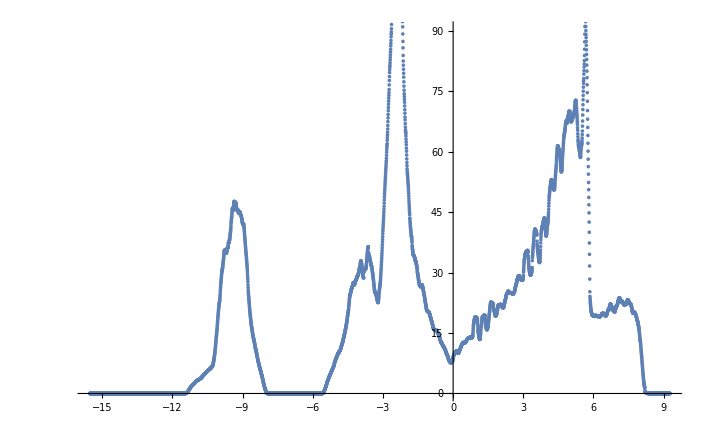

```mathematica
ListPlot@Interpolation[elData[[1]][[1]]]
```

```mathematica
Interpolation[elData[[1]][[1]]][x]Minimize[x.{1,2,3},x∈ℛ]
```

```mathematica
elData//Dimensions
```

{6,7,4961,2}

```mathematica
Table[Interpolation[elData[[1]][[1]]][0],{}]
```

8.84081

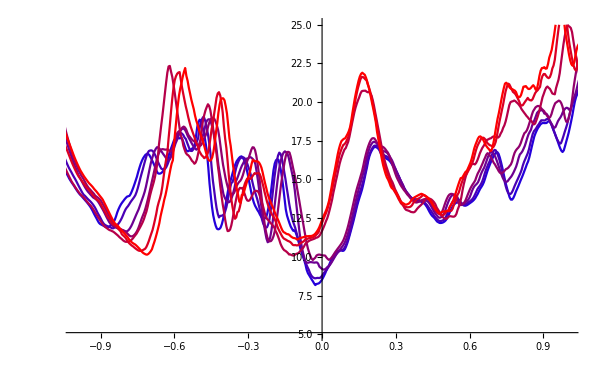

```mathematica
elDataNoShift1=Table[Table[MovingAverage[Transpose@{Transpose[objects[[j]][[i]]][[1]],Transpose[objects[[j]][[i]]][[2]]},10
],{i,1,objects[[j]]//Length}],{j,1,Length@objects}];
ListLinePlot[elDataNoShift1[[5]],PlotRange->{{-1,1},{5,25}},PlotStyle->Table[Blend[{Blue,Red},i/7],{i,1,7}]]
```

```mathematica
elDataNoShift=Table[Table[MovingAverage[Transpose@{Transpose[objects[[j]][[i]]][[1]],Transpose[objects[[j]][[i]]][[2]]},10],{i,1,objects[[j]]//Length}],{j,1,Length@objects}];
efermidata=Table[Table[{vols[[i]],Interpolation[elDataNoShift[[j]][[i]]][0]/64},{i,1,7}],{j,1,6}];
```

```mathematica
f[arg_]:=Style[arg,18]
names2={"Perf","B_2","B_3","U_2","U_3","U_4"};

styles=Flatten@Join[{Directive[{Thickness[0.012]}],Table[Directive[{Thickness[0.014],Dashing[0.02*i]}],{i,1,3}],Directive[{Thickness[0.015],Dotted}],Directive[{Thickness[0.015],DotDashed}]}];
```

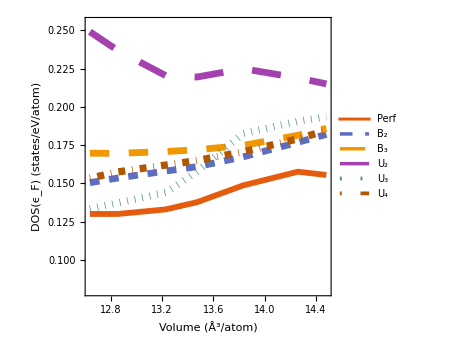

```mathematica
fermiStyle={AspectRatio->1.,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,True},FrameLabel->{Style["Volume (Å^3/atom)",18,Black],Style["DOS(ϵ_F) (states/eV/atom) ",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],PlotStyle->styles,ImageSize->350,PlotRange->{Automatic,{0.08,0.255}}};
efermi=ListLinePlot[efermidata,PlotLegends->Placed[LineLegend[Table[f[names2[[i]]],{i,1,Length@names2}],LegendLayout->{"Row",2}],{0.50,0.16}],fermiStyle]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/efermi.pdf",efermi]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/efermi.pdf

```mathematica
elData=Table[Table[MovingAverage[Transpose@{Transpose[objects[[j]][[i]]][[1]],Transpose[objects[[j]][[i]]][[2]]+50*(vols[[i]]-vols[[1]])},30],{i,1,objects[[j]]//Length}],{j,1,Length@objects}];
```

```mathematica
ListLinePlot[elData[[1]],Evaluate@plotStyle];
```

```mathematica
plotStyle={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,None},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS ",18,Black]},PlotStyle->Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->450,PlotRange->{{-6,6},Automatic}};
```

```mathematica
plotStyle1={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Black]},PlotLabels->{Placed[Style["a",18,Black],{0.38,0.74}]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{-5.5,6},All}};
plotStyle2={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->{Placed[Style["b",18,Black],{0.387,0.86}]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{-5.5,6},{0,240}}};
plotStyle3={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->{Placed[Style["c",18,Black],{0.388,0.88}]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{-5.5,6},{0,240}}};
plotStyle4={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ϵ-ϵ_F (eV)",18,Black],Style["DOS",18,Black]},PlotLabels->{Placed[Style["d",18,Black],{0.386,0.867}]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->387,PlotRange->{{-5.5,6},{0,240}}};
plotStyle5={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ϵ-ϵ_F (eV)",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->{Placed[Style["e",18,Black],{0.39,0.92}]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->387,PlotRange->{{-5.5,6},{0,240}}};
plotStyle6={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ϵ-ϵ_F (eV)",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->{Placed[Style["f",18,Black],{0.386,0.796}]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->387,PlotRange->{{-5.5,6},{0,220}}};


plotStyles={plotStyle1,plotStyle2,plotStyle3,plotStyle4,plotStyle5,plotStyle6};
```

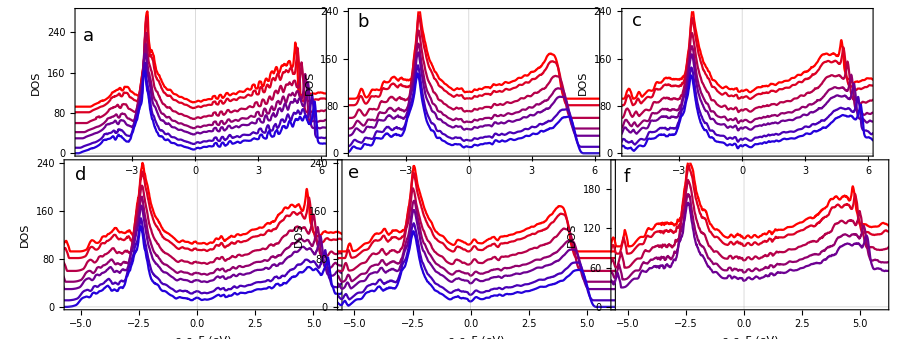

```mathematica
elgridplot=GraphicsGrid[Partition[Table[ListLinePlot[Reverse@elData[[i]],Evaluate@plotStyles[[i]]],{i,1,6}],3],Spacings->{-90,-30}]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/el-dos.pdf",elgridplot]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/el-dos.pdf

```mathematica
plotStyle={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,None},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS ",18,Black]},PlotStyle->Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->450,PlotRange->{{-1,1},{0,42}}};
GraphicsGrid[Partition[Table[ListLinePlot[elData[[i]],Evaluate@plotStyle],{i,1,6}],2]];
```

5

1

0.5

22

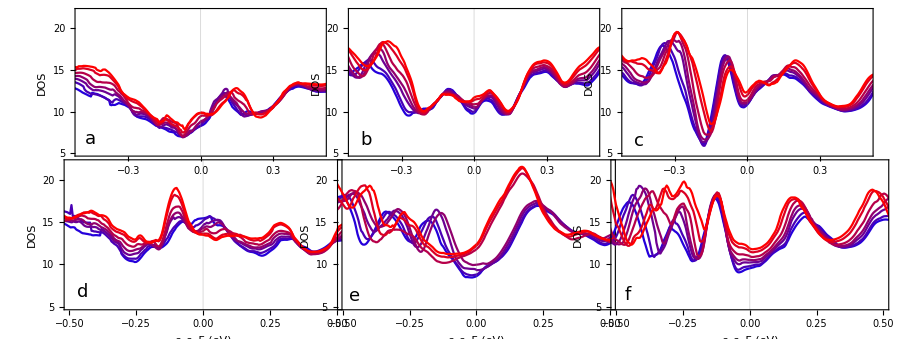

```mathematica
e=5
c=1;d=1
b=0.5
a=22
plotStyle1={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Black]},PlotLabels->Placed[{Style["a",18,Black]},{c*0.6074,d*0.036}],PlotStyle->Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{-b,b},{e,a}}};
plotStyle2={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->Placed[{Style["b",18,Black]},{c*0.611,d*0.048}],PlotStyle->Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{-b,b},{e,a}}};
plotStyle3={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->Placed[{Style["c",18,Black]},{c*0.611,d*0.048}],PlotStyle->Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{-b,b},{e,a}}};
plotStyle4={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ϵ-ϵ_F (eV)",18,Black],Style["DOS",18,Black]},PlotLabels->Placed[{Style["d",18,Black]},{c*0.611,d*0.048}],PlotStyle->Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->387,PlotRange->{{-b,b},{e,a}}};
plotStyle5={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ϵ-ϵ_F (eV)",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->Placed[{Style["e",18,Black]},{c*0.612,d*0.05}],PlotStyle->Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->387,PlotRange->{{-b,b},{e,a}}};
plotStyle6={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ϵ-ϵ_F (eV)",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->Placed[{Style["f",18,Black]},{c*0.612,d*0.048}],PlotStyle->Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->387,PlotRange->{{-b,b},{e,a}}};

plotStyles={plotStyle1,plotStyle2,plotStyle3,plotStyle4,plotStyle5,plotStyle6};
elData=Table[Table[MovingAverage[Transpose@{Transpose[objects[[j]][[i]]][[1]],Transpose[objects[[j]][[i]]][[2]]+0*(vols[[i]]-vols[[1]])},15],{i,1,objects[[j]]//Length}],{j,1,Length@objects}];

elgridplotsmall=GraphicsGrid[Partition[Table[ListLinePlot[elData[[i]],Evaluate@plotStyles[[i]]],{i,1,6}],3],Spacings->{-90,-30},PlotRange->{{-1,1},Automatic}]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/el-dos-small.pdf",elgridplotsmall]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/el-dos-small.pdf

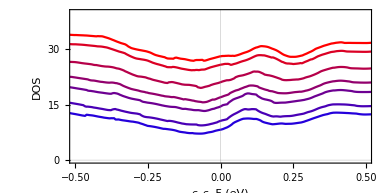

```mathematica
plotStyle6={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ϵ-ϵ_F (eV)",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->{Placed[Style["d",18,Black],{0,13}]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->387,PlotRange->{{-0.5,0.5},{0,a}}};
ListLinePlot[Reverse@elData[[1]],plotStyle6]
```

40

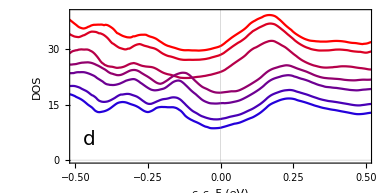

```mathematica
a=40
plotStyle6={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["ϵ-ϵ_F (eV)",18,Black],Style["DOS",18]},PlotLabels->Placed[{Style["d",20,Black]},{0.574,-0.088}],PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->387,PlotRange->{{-0.5,0.5},{0,a}}};
ListLinePlot[Reverse@elData[[5]],plotStyle6]
```

```mathematica
5
```

```mathematica
elData=Table[Table[MovingAverage[Transpose@{Transpose[objects[[j]][[i]]][[1]],Transpose[objects[[j]][[i]]][[2]]+0*(vols[[i]]-vols[[1]])},15],{i,1,objects[[j]]//Length}],{j,1,Length@objects}];
```

20

0.5

1

1

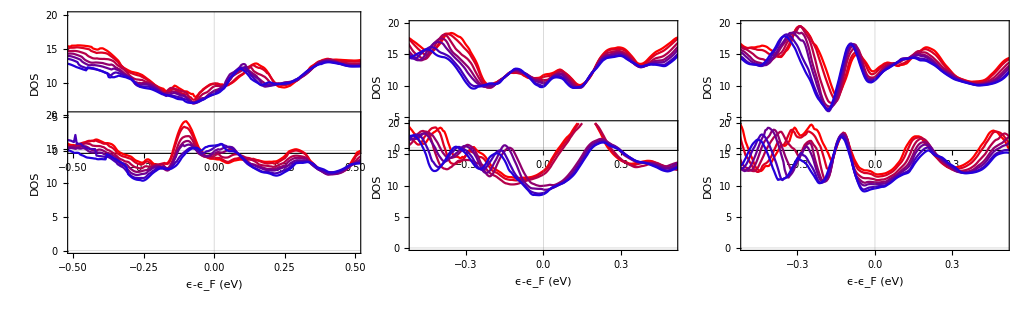

```mathematica
a=20
b=0.5
c=1
d=1
plotStyle1={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["",18,Black],Style["DOS",18,Black]},PlotLabels->Placed[{Style["a",18,Black]},{c*0.566,d*-0.065}],PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->{382,382},PlotRange->{{-b,b},{0,a}}};
plotStyle2={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->Placed[{Style["b",18,Black]},{c*0.570,d*-0.088}],PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->{350,350},PlotRange->{{-b,b},{0,a}}};
plotStyle3={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->Placed[{Style["c",18,Black]},{c*0.570,d*-0.088}],PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->{350,350},PlotRange->{{-b,b},{0,a}}};
plotStyle4={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["ϵ-ϵ_F (eV)",18,Black],Style["DOS",18,Black]},PlotLabels->Placed[{Style["d",18,Black]},{c*0.570,d*-0.088}],PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->{382,382},PlotRange->{{-b,b},{0,a}}};
plotStyle5={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ϵ-ϵ_F (eV)",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->Placed[{Style["e",18,Black]},{c*0.574,d*-0.088}],PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->{350,350},PlotRange->{{-b,b},{0,a}}};
plotStyle6={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ϵ-ϵ_F (eV)",18,Black],Style["DOS",18,Opacity[0]]},PlotLabels->Placed[{Style["f",18,Black]},{c*0.571,d*-0.088}],PlotStyle->Reverse@Table[Blend[{Blue,Red},i/7],{i,1,7}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->{350,350},PlotRange->{{-b,b},{0,a}}};

plotStyles={plotStyle1,plotStyle2,plotStyle3,plotStyle4,plotStyle5,plotStyle6};


elgridplotsmall=GraphicsGrid[Partition[Table[ListLinePlot[Reverse@elData[[i]],Evaluate@plotStyles[[i]]],{i,1,6}],3],Spacings->{-45,-220},PlotRange->{{-1,1},Automatic}]
```